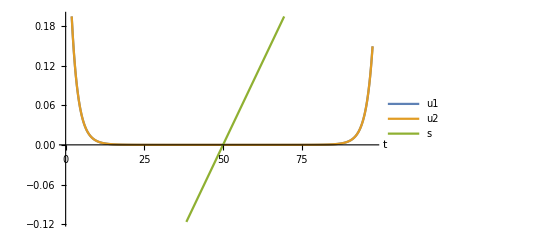

```mathematica
f[s_,ε_]:=s;
eps =10^-2; s0=-0.5;tmax=1.95-s0/eps;
system = {u1'[t]==f[s[t],ε] u1[t], u2'[t]==(-ε^α π^2+f[s[t],ε])u2[t], s'[t]==ε, u1[0]==0.5, u2[0]==0.5,s[0]==s0}/. {α->4.0, ε->eps};
sol = NDSolve[system,{s[t],u1[t],u2[t]},{t,0,tmax}];
(*ParametricPlot3D[{s[t], u1[t], u2[t]}/.sol, {t, 0, tmax}, AxesLabel->{s,u1,u2}]*)
Plot[{u1[t]/.sol,u2[t]/.sol,s[t]/.sol}, {t, 0, tmax},PlotLegends->{u1, u2, s},AxesLabel->{t}]
```

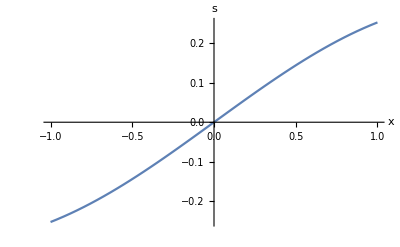

NDSolve::ndnl: Endpoint -750. s0 in {t,0.,-750. s0} is not a real number.

Plot::plln: Limiting value -750. s0 in {t,0,-750. s0} is not a machine-sized real number.

NDSolve::ndnl: Endpoint -750. s0 in {t,0.,-750. s0} is not a real number.

Plot::plln: Limiting value -750. s0 in {t,0,-750. s0} is not a machine-sized real number.

NDSolve::ndnl: Endpoint -750. s0 in {t,0.,-750. s0} is not a real number.

Plot::plln: Limiting value -750. s0 in {t,0,-750. s0} is not a machine-sized real number.

NDSolve::ndnl: Endpoint -750. s0 in {t,0.,-750. s0} is not a real number.

Plot::plln: Limiting value -750. s0 in {t,0,-750. s0} is not a machine-sized real number.

```mathematica
ClearAll[f, mu11,mu12,mu21,mu22,u1,u2,s];
turningCurve[x_] = 3/10 Sin[x];
f[x_,s_, ε_]:= s-turningCurve[x];
Plot[turningCurve[x],{x,-1, 1},PlotLegends->"turning curve",AxesLabel->{x, s}]
s0=-0.5;
mu11[s_,ε_]:=2^(-1/2)Integrate[f[x, s, ε],{x, -1, 1}];
mu21[s_,ε_]:=2^(-1/2)Integrate[f[x, s, ε] Cos[π x],{x, -1, 1}];
mu22[s_,ε_]:=2^(-1/2)Integrate[f[x, s, ε] Cos[π x] Cos[π x],{x, -1, 1}];

Manipulate[(system ={u1'[t]==mu11[s[t], ε] u1[t] + mu21[s[t], ε]u2[t], u2'[t]==-ε^α π^2 u2[t]+mu21[s[t], ε]u1[t]+mu22[s[t],ε]u2[t],s'[t]==ε, u1[0]==u10, u2[0]==u20,s[0]==s0};sol = NDSolve[system /. {α->alpha, ε->eps},{s[t],u1[t],u2[t]},{t,0,2.5-s0/eps},Method->"BDF"];
(*ParametricPlot3D[{s[t], u1[t], u2[t]}/.sol, {t, 0, tmax}, AxesLabel->{s,u1,u2}]*)
Column[{Plot[{u1[t]/.sol,u2[t]/.sol,s[t]/.sol}, {t, 0, 2.5-s0/eps},PlotLegends->{u1, u2, s},AxesLabel->{t}], system}]), {eps, {1/300, 1/200,1/150, 1/100}},{u10, -1.0, 1.0, 0.1},{u20, -1.0, 1.0, 0.1},{alpha, 0.5, 3.0, 0.2} ]
```

```mathematica
Manipulate[(system ={ε u1'[t]==s[t] u1[t],ε u2'[t]==-ε^α π^2 u2[t]+s[t]u2[t],s'[t]==1, u1[0]==u10, u2[0]==u20,s[0]==s0};sol = NDSolve[{system, WhenEvent[u1[t]>=10 ||u2[t] >=10, "StopIntegration"]} /. {α->alpha, ε->eps, s0->-0.5},{s[t],u1[t],u2[t]},{t,0,1.2}];
(*ParametricPlot3D[{s[t], u1[t], u2[t]}/.sol, {t, 0, tmax}, AxesLabel->{s,u1,u2}]*)
Column[{Plot[{u1[t]/.sol,u2[t]/.sol,s[t]/.sol},{t,0, 1.2},PlotLegends->{u1, u2, s},AxesLabel->{t}], system}]), {eps, {1/300, 1/200,1/150, 1/100}},{u10, 0.1, 1.0, 0.1},{u20, 0.1, 1.0, 0.1},{alpha, 0.5, 3.0, 1.2} ]
```

```mathematica
eta[k_,i_,j_]:=Integrate[Cos[(i+j-2)Pi x]Cos[(k-1)Pi x],{x, 0, 1}]+Integrate[Cos[(i-j)Pi x] Cos[(k-1)Pi x],{x, 0, 1}]
```

```mathematica
{eta[2,2,2],eta[2,2,2],eta[2,2,3],eta[2,2,4]}
```

```mathematica
{0,1/2,0,1/2}
```

```mathematica
Scan[Print[eta[4,2,#]]&,{1, 2,3,4}]
```

0

0

1/2

0

```mathematica
jac3 ={{s-1,0,0},{-1,s,-1/2},{0,-1/2,s}};
jac3//MatrixForm
Eigenvalues[jac3]//Simplify
```

(-1+s | 0 | 0
-1 | s | -1/2
0 | -1/2 | s)

{-1+s,-1/2+s,1/2+s}

```mathematica
jac4={{s-1,0,0,0},{-1,s,-1/2,0},{0,-1/2,s,-1/2},{0,0,-1/2,s}};
jac4//MatrixForm
Eigenvalues[jac4]//Simplify
```

(-1+s | 0 | 0 | 0
-1 | s | -1/2 | 0
0 | -1/2 | s | -1/2
0 | 0 | -1/2 | s)

{-1+s,s,-1/(√2)+s,1/(√2)+s}

```mathematica
ClearAll[u1,u2,u3,ε,t,s0];DSolve[{ε u1'[t]==( t + s0 - 1)u1[t],ε u2'[t]==(√2 ε^α Subscript[b, 2]/a^(5/2)+t+s0)u2[t]-u1[t]-1/2 u3[t],ε u3'[t]==(√2 ε^α Subscript[b, 3]/a^(5/2)+ t+s0)u3[t]-1/2 u2[t],u1[0]==u10,u2[0]==u20,u3[0]==u30},{u1,u2,u3},t]//FullSimplify
```